# II. Normal Distribution

## Författare

Stefan Josefsson, stejos@kth.se
Joe Huldén, joeda@kth.se

## Summering

Task1. Study the average t̄=1/n ∑_(k=1)^n t_k of n=20 interarrival times. 
Plot the absolute error of the pdf_(t̄)(t) and the cdf_(t̄)(t) using the normal approximation. 
Make also a plot of the relative error of P(t̄>x), μ-2σ/√n<x<μ+2σ/√n Conclusion? Is the approximation always useful?

Hint: The sum of iid exponential rvs has a well-known distribution, which is built-in in Mathematica, ErlangDistribution[n,λ] or GammaDistribution[n,1/λ].

Task2. Study the number of incoming calls during one hour. 
Plot the absolute and relative error of the probability function using normal approximation. Conclusion?

Hint: What is the distribution of the number of events in a certain time interval, e.g 1h, if the time between the events is exponential?

Task1. Answer and Conclusion: 
Absolute Error determines how far away we are from target. |tested-claimed| = A.E.
Relative Error determines the error in percentage. A.E. / claimed = R.E. in %.

The normal approximation is reasonable if both np ≥10 and n(1-p)≥10.

Task2. Answer and Conclusion:

## Mattematiskt tillvägagångsätt

Täthetsfunktionen för summan av tiden mellan n stycken samtal kan beskrivas av  pdf_n(s)=∫_(∀t) pdf_1(s-t)pdf_(n-1)(t)dt. Vi är intresserade av snittiden mellan samtalen vid n samtal varför vi får täthetsfunktionen pdf_n(s)=∫_(∀t) pdf_1((s-t) / k)pdf_(n-1)(t / k)dt, k=20. Integration över denna täthetsfunktionen ger oss fördelningsfunktionen för valt intervall. Denna beskriver då sannolikheten för att snittiden mellan två samtal understiger något värde.
Normalapproximation av täthetsfunktionen erhålles med hjälp av: 1/n∑_(i=1)^n 𝔵_i=𝔵̄(\[Distributed])^CLT N(μ,σ) Denna säger att snittiden mellan samtalen givet n stokastiska variabler kan skattas till en normalfördelning med  μ=1/n∑_(i=1)^n E[𝔵_i],σ^2=^(indep.)1/n^2∑_(i=1)^n V[𝔵_i]
Men väntevärdet är redan kännt och uppgår för alla stokastiska variabler till 3. Standardavvikelsen vidare beräknas genom V(X) = E[(X-my)^2]. Denna normalapproximation N(μ,σ) är den approximerade täthetsfunktionen. Integration över denna ger då fördelningsfunktionen. Både den exakta täthetsfunktion, fördelningsfunktion samt approximerade täthetsfunktion, fördelningsfunktion krävs för beräkning av det absoluta och relativa felet. Det absoluta felet uppgår till absolutbeloppet av differensen mellan dessa funktioner. Det relativa felet är det absoluta felet genom den exakta täthetsfunktion resp fördelningsfunktion.
 
Sannolikheten kopplad till antalet samtal under inkomna under en timmas period skall beräknas. Sannolikheten för att ett samtal har skett under en timma är detsamma som att betrakta fördelningsfunktionen kopplad till en stokastisk variabel i punkten t = 60. Sannolikheten för att två samtal skett under en timma är detsamma som att betrakta fördelningsfunktion kopplad till att summan av två stokastiska variabler, med given fördelning och väntevärde, i punk t = 60. Täthetsfunktion för summan av n stycken oberoende stokastiska variabler är   pdf_n(s)=∫_(∀t) pdf_1(s-t)pdf_(n-1)(t)dt. Integration över detta uttryck ger fördelningsfunktionen. Värdet på fördelningsfunktionen i punkten t = 60 beskriver då sannolikheten för n stycken samtal för respektive fördelningsfunktion.
Summan över n stycken oberoende stokastiska variabler kan approximeras med ∑_(i=1)^n 𝔵_i==𝔰(\[Distributed])^CLT N(n μ,√n σ). Integration över Normalkurvan ger då en approximerad fördelningsfunktion kopplad till n stycken samtal. Värdet på denna fördelningsfunktion i punkten t = 60 beskriver då den approximerade sannolikheten för n stycken samtal.

## Diskussion

Varför ser skiten ut som det gör....

## Grafer

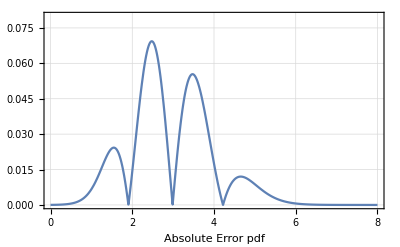
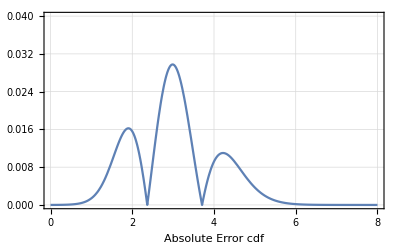
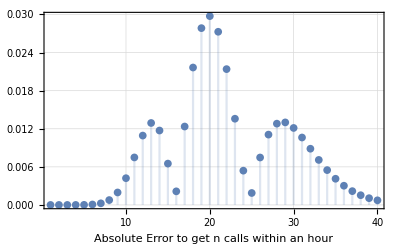
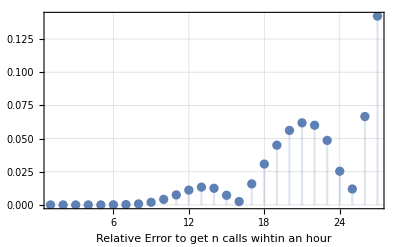

## Kod

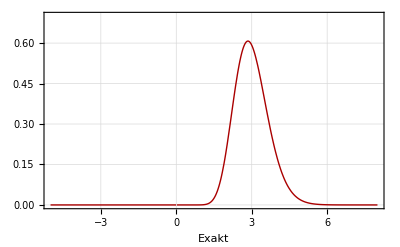

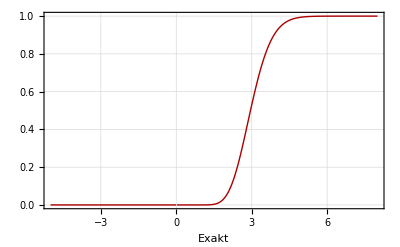

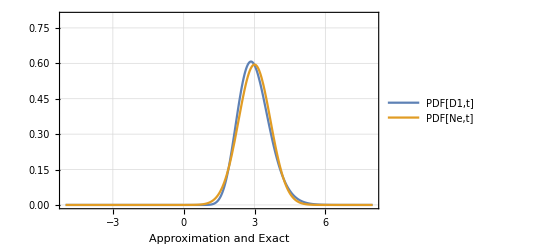

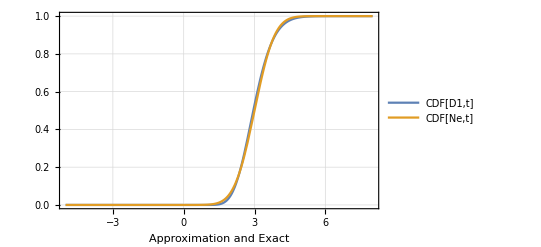

-Graphics-

-Graphics-

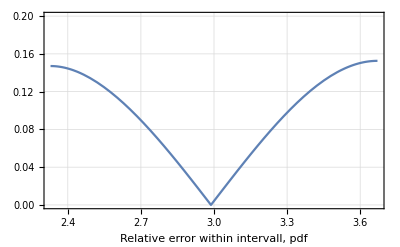

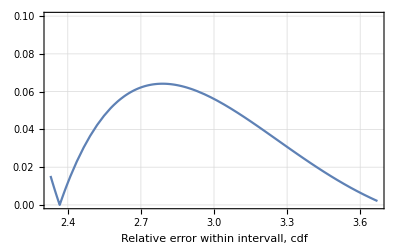

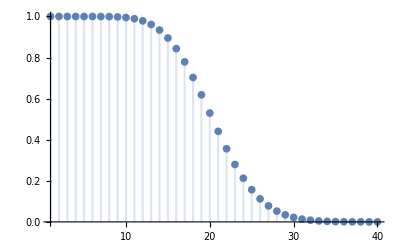

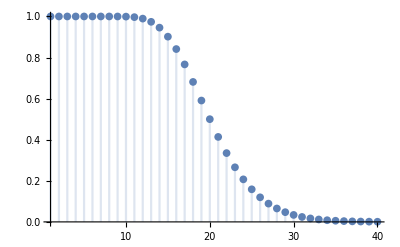

-Graphics-

-Graphics-

```mathematica
ClearAll["`*"]
σ = 3;

n = 20;
Subscript[λ, 1] = n/σ; (*testar detta nu*)
Subscript[λ, 2] = 1/σ;
D1 = ErlangDistribution[20,Subscript[λ, 1]];
μ = StandardDeviation[ErlangDistribution[1,Subscript[λ, 2]]];

(*exakt*)
p1=Plot[PDF[D1,t],{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, 1][t]]},PlotStyle->Directive[Darker[Red],Thick],PlotRange->{0,0.70},Frame->True,FrameLabel-> "Exakt",GridLines->Automatic]
p2=Plot[CDF[D1,t],{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[Subscript[cdf, 1][t]]},PlotStyle->Directive[Darker[Red],Thick], PlotRange->{0,1},Frame->True,FrameLabel-> "Exakt",GridLines->Automatic]

(*approximation med exakt*)
Ne = NormalDistribution[μ, σ/√n];
Plot[{PDF[D1,t],PDF[Ne,t]},{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->{0,0.8}, Frame->True,FrameLabel-> "Approximation and Exact",GridLines->Automatic,PlotLegends->"Expressions"]
Plot[{CDF[D1,t],CDF[Ne,t]},{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}, PlotRange->{0,1},Frame->True,FrameLabel-> "Approximation and Exact",GridLines->Automatic,PlotLegends->"Expressions"]

(*absoluta felet hela intervall*)
Plot[{Abs[PDF[D1,t]-PDF[Ne,t]]},{t,0,8},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->{0,0.08},Frame->True,FrameLabel-> "Absolute Error pdf",GridLines->Automatic]
Plot[{Abs[CDF[D1,t]-CDF[Ne,t]]},{t,0,8},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}, PlotRange->{0,0.04},Frame->True,FrameLabel-> "Absolute Error cdf",GridLines->Automatic]

(*relativa felet, svnärt intervall*)
Plot[{(Abs[PDF[D1,t]-PDF[Ne,t]])/PDF[D1,t]},{t,μ - σ/√20,μ + σ/√20},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->{0,0.20},Frame->True,FrameLabel-> "Relative error within intervall, pdf",GridLines->Automatic]
Plot[{(Abs[CDF[D1,t]-CDF[Ne,t]])/CDF[D1,t]},{t,μ - σ/√20,μ + σ/√20},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}, PlotRange->{0,0.10},Frame->True,FrameLabel-> "Relative error within intervall, cdf",GridLines->Automatic]

(*Task 2*)
time = 60;
(*Börjar med den exakta*)
(*Visar exakta sannolikheten att få n samtal inom loppet av en timma*)
F[n_]:=N[CDF[ErlangDistribution[n,1/σ], 60],100];
DiscretePlot[F[n],{n,1,40}]

(*Visar approximerade sannolikheten att få n samtal inom loppet av en timma*)
Fapprox[n_]:=N[CDF[NormalDistribution[n*μ, σ*√n], 60],100];
DiscretePlot[Fapprox[n],{n,1,40}]
(*Visar absoluta felet för att få n samtal inom loppet av en timma*)
DiscretePlot[Abs[Fapprox[n] - F[n]],{n,1,40},Frame->True,FrameLabel-> "Absolute Error to get n calls within an hour",GridLines->Automatic]
(*Visar relativa felet för att få n samtal inom loppet av en timma*)
DiscretePlot[Abs[Fapprox[n] - F[n]] / F[n],{n,1,27},Frame->True,FrameLabel-> "Relative Error to get n calls wihtin an hour",GridLines->Automatic]
```